```mathematica
SetDirectory["E:\\Python\\Software\\Apps\\linacCentring\\"]
```

E:\Python\Software\Apps\linacCentring

## X

```mathematica
data=Rest[Import["20180823-210831_LinacCentring_Linac1_X_8000_16000_rawData.csv"]];
```

```mathematica
ListPlot3D[Select[data[[All,{1,2,-1}]],#[[-1]]=!=20.&]]
```

-Graphics3D-

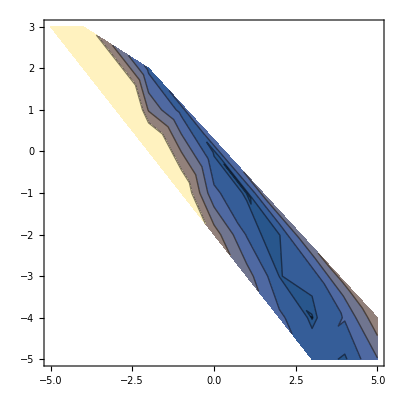

```mathematica
ListContourPlot[Select[data[[All,{2,1,-1}]],#[[-1]]=!=20.&],Contours->{0,.1,.2,.3,1,5,10,15,20}]
```

```mathematica
fit=Fit[ToExpression/@{{"-0.5686","0.5344"},{"0.1289","-0.09631"},{"0.8567","-0.8484"},{"1.463","-1.6"},{"1.857","-2.352"},{"2.464","-3.056"},{"2.949","-3.614"},{"3.495","-4.366"}},{1,x},x]
```

0.0262516-1.23435 x

```mathematica
Transpose[{x,fit}/.{x->Range[0,3,.5]}]
```

{{0.,0.0262516},{0.5,-0.590922},{1.,-1.2081},{1.5,-1.82527},{2.,-2.44244},{2.5,-3.05962},{3.,-3.67679}}

## Y

```mathematica
data=Rest[Import["20180823-215558_LinacCentring_Linac1_Y_8000_16000_rawData.csv"]];
```

```mathematica
ListPlot3D[Select[data[[All,{1,2,-1}]],#[[-1]]=!=20.&]]
```

-Graphics3D-

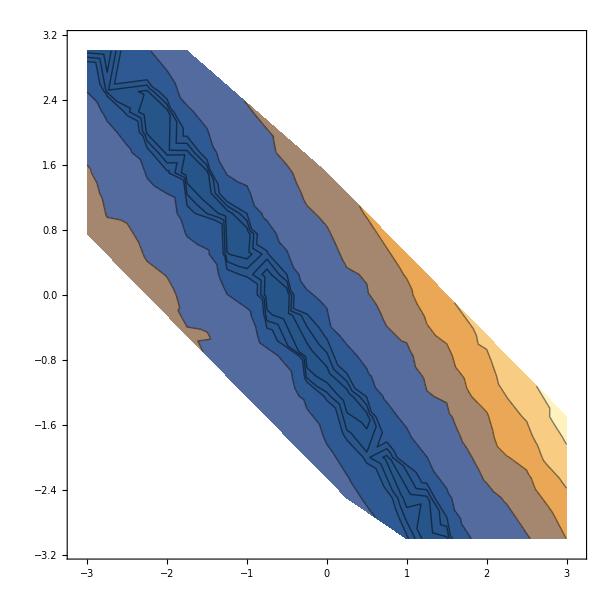

```mathematica
ListContourPlot[Select[data[[All,{2,1,-1}]],#[[-1]]=!=20.&],Contours->{0,.1,.2,.3,1,5,10,15,20}]
```

```mathematica
fit=Fit[ToExpression/@{{"-2.147","2.132"},{"-1.117","0.6912"},{"-0.6019","-0.1078"},{"-0.03417","-0.9278"},{"0.5756","-1.832"},{"1.07","-2.484"},{"1.322","-2.862"}},{1,x},x]
```

-0.962529-1.44488 x

```mathematica
Transpose[{x,fit}/.{x->Range[-2,0,.5]}]
```

{{-2.,1.92723},{-1.5,1.20479},{-1.,0.482348},{-0.5,-0.240091},{0.,-0.962529}}

```mathematica
x = k lq qx ld
```

```mathematica
14.9*0.125*0.4*3
```

2.235

## Quad Align 24-8-18 (SOLS Off)

```mathematica
SetDirectory["\\\\fed.cclrc.ac.uk\\Org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\08\\24"]
```

\\fed.cclrc.ac.uk\Org\NLab\ASTeC\Projects\VELA\Work\2018\08\24

```mathematica
xdata=Drop[Import["./203956__QuadAlignX.dat"],7];
```

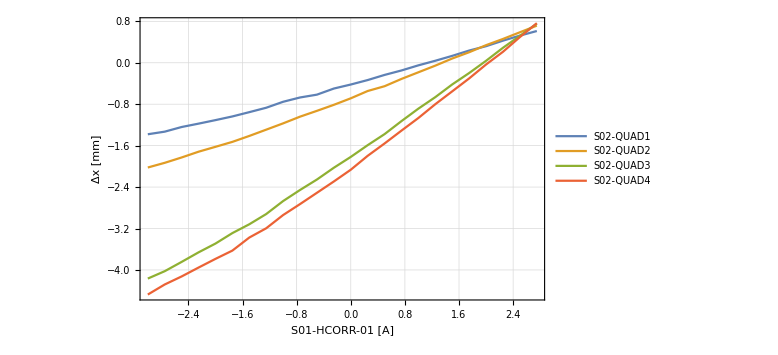

Quad_X_Offset_vs_HCORR_minimised_linac_kick.png

```mathematica
ListLinePlot[Transpose[Partition[xdata,4]][[All,All,{1,6}]],PlotLegends->Placed[LineLegend[Transpose[Partition[xdata,4]][[All,1,5]],LegendFunction->Panel],Scaled[{0.8,0.2}]],Frame->True,FrameLabel->{"S01-HCORR-01 [A]","Δx [mm]"},ImageSize->Large,GridLines->Automatic,BaseStyle->{FontSize->14}]
Export["Quad_X_Offset_vs_HCORR_minimised_linac_kick.png",%,ImageResolution->200]
```

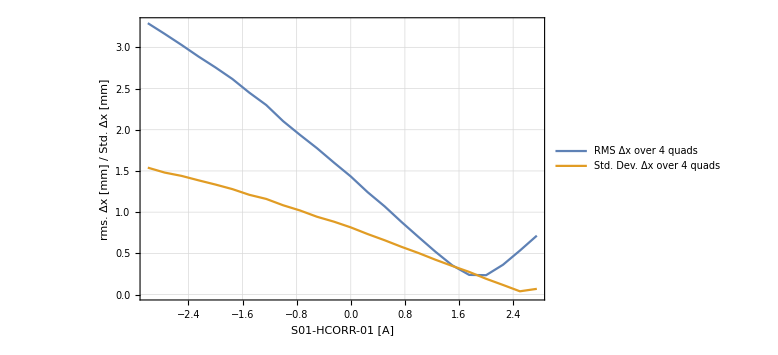

```mathematica
ListLinePlot[{{#[[1,1]],RootMeanSquare[#[[All,2]]]}&/@Partition[xdata,4][[All,All,{1,6}]],
{#[[1,1]],StandardDeviation[#[[All,2]]]}&/@Partition[xdata,4][[All,All,{1,6}]]},Frame->True,PlotLegends->Placed[LineLegend[{"RMS Δx over 4 quads","Std. Dev. Δx over 4 quads"},LegendFunction->Panel],Scaled[{0.8,0.82}]],FrameLabel->{"S01-HCORR-01 [A]","rms. Δx [mm] / Std. Δx [mm]"},ImageSize->Large,GridLines->Automatic,BaseStyle->{FontSize->14}]
Export["Combined_Quad_X_Offset_vs_HCORR_minimised_linac_kick.png",%,ImageResolution->200]
```

```mathematica
Sort[{#[[1,1]],RootMeanSquare[#[[All,2]]]}&/@Partition[xdata,4][[All,All,{1,6}]],#1[[2]]<#2[[2]]&]
```

{{2.,0.234758},{1.75,0.238484},{1.5,0.354714},{2.25,0.361464},{1.25,0.520473},{2.5,0.533421},{1.,0.699193},{2.75,0.714583},{0.75,0.880598},{0.5,1.07049},{0.25,1.24167},{0.,1.43318},{-0.25,1.6021},{-0.5,1.7764},{-0.75,1.93709},{-1.,2.10411},{-1.25,2.30019},{-1.5,2.45029},{-1.75,2.6159},{-2.,2.75599},{-2.25,2.88794},{-2.5,3.02833},{-2.75,3.16299},{-3.,3.29321}}

```mathematica
(0.0262516-1.25*2)
```

-2.47375

```mathematica
ydata=Drop[Import["./203956__QuadAlignY.dat","Table"],7];
```

```mathematica
data=ydata;
```

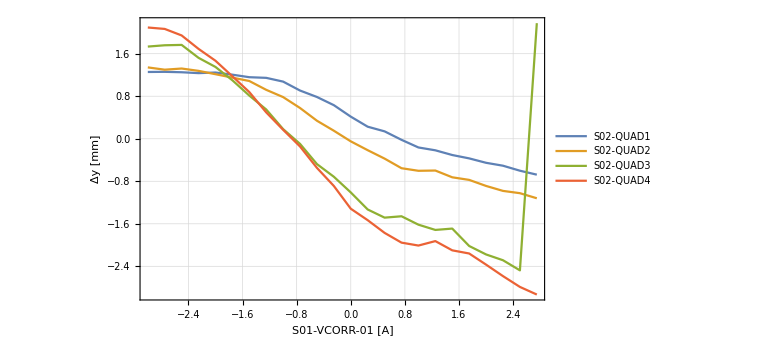

Quad_Y_Offset_vs_VCORR_minimised_linac_kick.png

```mathematica
ListLinePlot[Transpose[Partition[data,4]][[All,All,{3,7}]],PlotLegends->Placed[LineLegend[Transpose[Partition[data,4]][[All,1,5]],LegendFunction->Panel],Scaled[{0.8,0.2}]],Frame->True,FrameLabel->{"S01-VCORR-01 [A]","Δy [mm]"},ImageSize->Large,GridLines->Automatic,BaseStyle->{FontSize->14}]
Export["Quad_Y_Offset_vs_VCORR_minimised_linac_kick.png",%,ImageResolution->200]
```

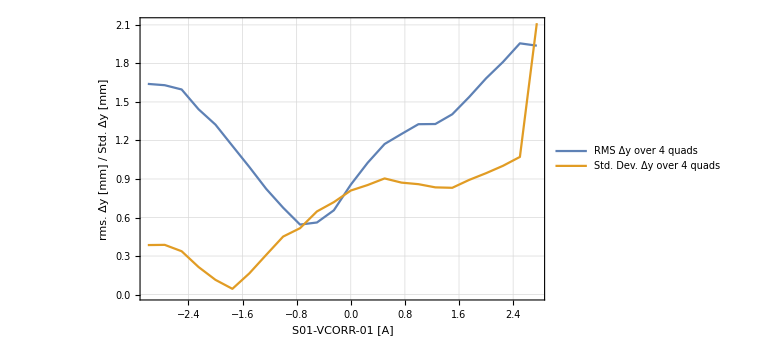

Combined_Quad_Y_Offset_vs_VCORR_minimised_linac_kick.png

```mathematica
ListLinePlot[{{#[[1,1]],RootMeanSquare[#[[All,2]]]}&/@Partition[data,4][[All,All,{3,7}]],
{#[[1,1]],StandardDeviation[#[[All,2]]]}&/@Partition[data,4][[All,All,{3,7}]]},Frame->True,PlotLegends->Placed[LineLegend[{"RMS Δy over 4 quads","Std. Dev. Δy over 4 quads"},LegendFunction->Panel],Scaled[{0.8,0.18}]],FrameLabel->{"S01-VCORR-01 [A]","rms. Δy [mm] / Std. Δy [mm]"},ImageSize->Large,GridLines->Automatic,BaseStyle->{FontSize->14}]
Export["Combined_Quad_Y_Offset_vs_VCORR_minimised_linac_kick.png",%,ImageResolution->200]
```

```mathematica
Sort[{#[[1,1]],RootMeanSquare[#[[All,2]]]}&/@Partition[data,4][[All,All,{3,7}]],#1[[2]]<#2[[2]]&]
```

{{-0.75,0.544866},{-0.5,0.561246},{-0.25,0.656316},{-1.,0.676511},{-1.25,0.822941},{0.,0.855707},{-1.5,0.993907},{0.25,1.02662},{-1.75,1.1581},{0.5,1.17248},{0.75,1.25057},{-2.,1.32332},{1.,1.32674},{1.25,1.32811},{1.5,1.40397},{-2.25,1.44296},{1.75,1.53845},{-2.5,1.59716},{-2.75,1.63041},{-3.,1.64063},{2.,1.68386},{2.25,1.81141},{2.75,1.93842},{2.5,1.95647}}

```mathematica
(-0.962529-1.44488*-0.75)
```

0.121131

## Quad Align 24-8-18 (SOLS On at +50A/-50A)

```mathematica
SetDirectory["\\\\fed.cclrc.ac.uk\\Org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\08\\24"]
```

\\fed.cclrc.ac.uk\Org\NLab\ASTeC\Projects\VELA\Work\2018\08\24

```mathematica
xdata=Drop[Import["./225608__QuadAlignX.dat"],1];
```

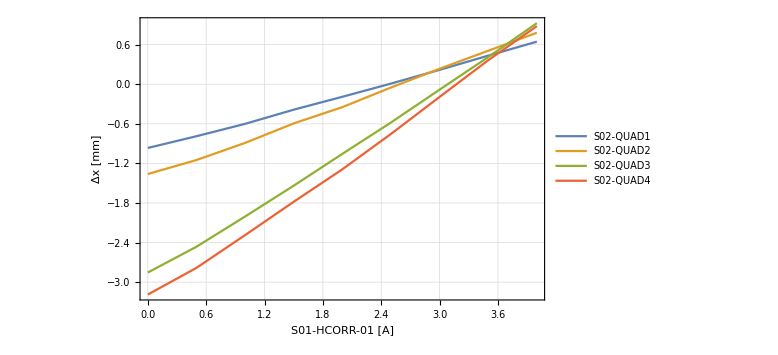

Quad_X_Offset_vs_HCORR_minimised_linac_kick_SOLS_ON.png

```mathematica
ListLinePlot[Transpose[Partition[xdata,4]][[All,All,{1,6}]],PlotLegends->Placed[LineLegend[Transpose[Partition[xdata,4]][[All,1,5]],LegendFunction->Panel],Scaled[{0.8,0.2}]],Frame->True,FrameLabel->{"S01-HCORR-01 [A]","Δx [mm]"},ImageSize->Large,GridLines->Automatic,BaseStyle->{FontSize->14}]
Export["Quad_X_Offset_vs_HCORR_minimised_linac_kick_SOLS_ON.png",%,ImageResolution->200]
```

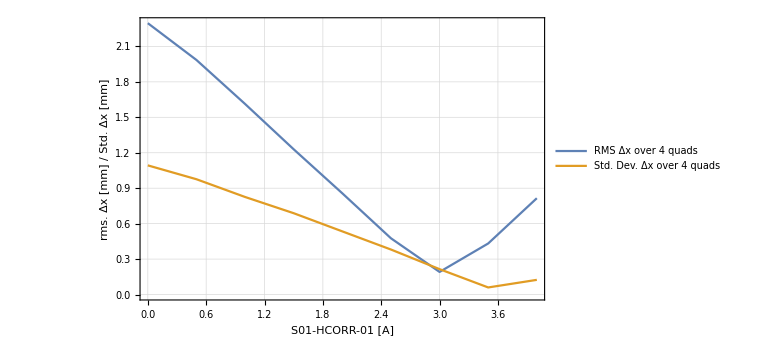

Combined_Quad_X_Offset_vs_HCORR_minimised_linac_kick_SOLS_ON.png

```mathematica
ListLinePlot[{{#[[1,1]],RootMeanSquare[#[[All,2]]]}&/@Partition[xdata,4][[All,All,{1,6}]],
{#[[1,1]],StandardDeviation[#[[All,2]]]}&/@Partition[xdata,4][[All,All,{1,6}]]},Frame->True,PlotLegends->Placed[LineLegend[{"RMS Δx over 4 quads","Std. Dev. Δx over 4 quads"},LegendFunction->Panel],Scaled[{0.8,0.82}]],FrameLabel->{"S01-HCORR-01 [A]","rms. Δx [mm] / Std. Δx [mm]"},ImageSize->Large,GridLines->Automatic,BaseStyle->{FontSize->14}]
Export["Combined_Quad_X_Offset_vs_HCORR_minimised_linac_kick_SOLS_ON.png",%,ImageResolution->200]
```

```mathematica
Sort[{#[[1,1]],RootMeanSquare[#[[All,2]]]}&/@Partition[xdata,4][[All,All,{1,6}]],#1[[2]]<#2[[2]]&]
```

{{3.,0.191353},{3.5,0.432291},{2.5,0.476162},{4.,0.815286},{2.,0.856664},{1.5,1.22924},{1.,1.61285},{0.5,1.98512},{0.,2.29656}}

```mathematica
(0.0262516-1.25*3)
```

-3.72375

```mathematica
ydata=Drop[Import["./225608__QuadAlignY.dat","Table"],1];
```

```mathematica
data=ydata;
```

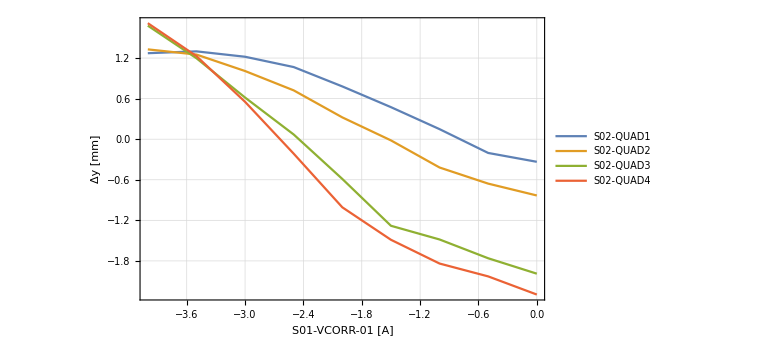

Quad_Y_Offset_vs_VCORR_minimised_linac_kick_SOLS_ON.png

```mathematica
ListLinePlot[Transpose[Partition[data,4]][[All,All,{3,7}]],PlotLegends->Placed[LineLegend[Transpose[Partition[data,4]][[All,1,5]],LegendFunction->Panel],Scaled[{0.8,0.2}]],Frame->True,FrameLabel->{"S01-VCORR-01 [A]","Δy [mm]"},ImageSize->Large,GridLines->Automatic,BaseStyle->{FontSize->14}]
Export["Quad_Y_Offset_vs_VCORR_minimised_linac_kick_SOLS_ON.png",%,ImageResolution->200]
```

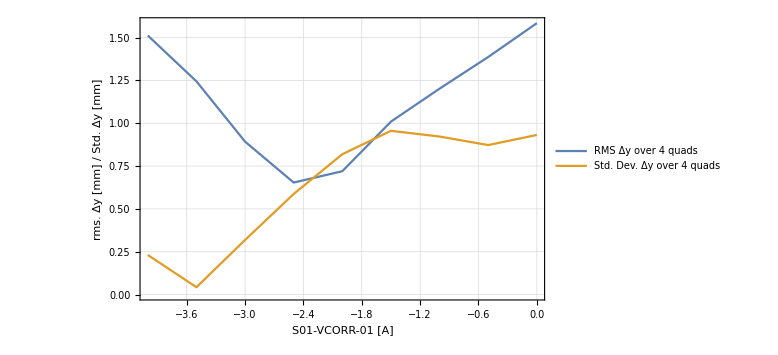

Combined_Quad_Y_Offset_vs_VCORR_minimised_linac_kick_SOLS_ON.png

```mathematica
ListLinePlot[{{#[[1,1]],RootMeanSquare[#[[All,2]]]}&/@Partition[data,4][[All,All,{3,7}]],
{#[[1,1]],StandardDeviation[#[[All,2]]]}&/@Partition[data,4][[All,All,{3,7}]]},Frame->True,PlotLegends->Placed[LineLegend[{"RMS Δy over 4 quads","Std. Dev. Δy over 4 quads"},LegendFunction->Panel],Scaled[{0.8,0.18}]],FrameLabel->{"S01-VCORR-01 [A]","rms. Δy [mm] / Std. Δy [mm]"},ImageSize->Large,GridLines->Automatic,BaseStyle->{FontSize->14}]
Export["Combined_Quad_Y_Offset_vs_VCORR_minimised_linac_kick_SOLS_ON.png",%,ImageResolution->200]
```

```mathematica
Sort[{#[[1,1]],RootMeanSquare[#[[All,2]]]}&/@Partition[data,4][[All,All,{3,7}]],#1[[2]]<#2[[2]]&]
```

{{-2.5,0.653845},{-2.,0.720034},{-3.,0.892608},{-1.5,1.0096},{-1.,1.20199},{-3.5,1.24461},{-0.5,1.38675},{-4.,1.51197},{0.,1.58424}}

```mathematica
(-0.962529-1.44488*-2.5)
```

2.64967